## 11_30_17

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

begin evaluations

Getting evaluation information:

```mathematica
$DurationInformation
```

{1}
 |  |  |  |

```mathematica
models=GroupBy[Dataset[$DurationInformation],#["FrameworkModel"]&]
```

Dataset[<>]

## 11_20_17

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
$DurationInformation
```

{1}
 |  |  |  |

```mathematica
models=GroupBy[Dataset[$DurationInformation],#["FrameworkModel"]&]
```

Dataset[<>]

## Old

## Install Dependencies

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"install_dep.m"}]];
```

```mathematica
InstallMongoDBLink[]
```

Installed MongoDBLink to /Library/Mathematica/Applications

## Run

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
$AccuracyInformation
```

{<|ID→59ffc48d008c598156f1e7d6,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffc507008c5981a9f4cc7f,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffc4cfca60cc5b378c6efa,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→59ffc582008c5981f6d38b63,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.55584,Top5→0.791|>,<|ID→59ffc605008c59831de29459,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.55584,Top5→0.791|>,<|ID→59ffc69d008c59836eb33a86,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.55584,Top5→0.791|>,<|ID→59ffc75e008c5983ba87b635,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.67754,Top5→0.88292|>,<|ID→59ffc7eb008c5984080b5680,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.67754,Top5→0.88292|>,<|ID→59ffc87c008c59845a7f184c,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.67754,Top5→0.88292|>,<|ID→59ffc91a008c5984a73f287d,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.67754,Top5→0.88292|>,<|ID→59ffc9d6008c5984fa1eaf2e,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.67754,Top5→0.88292|>,<|ID→59ffcac2008c5985530eb72f,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffcb99008c5985a589b49e,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffcc7e008c5985f460e5a3,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffcd5e008c5986457c4d53,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffce54008c5986999c18e4,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffcf7e008c5986ef73f557,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffd06d008c598744b3d6d1,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffd162008c598797f79e96,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffd263008c5987eedb2125,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffd379008c59884535d898,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffd4ce008c59899e0035ac,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffd5c4008c5989e761e3e2,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffd6b6008c598a32ae9178,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffd7b2008c598a7a332db9,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffd8c0008c598ac692c118,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→59ffd9ec008c598b155f72be,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.68084,Top5→0.88484|>,<|ID→59ffdb0c008c598b616883c4,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.68084,Top5→0.88484|>,<|ID→59ffdc2b008c598bb19207cd,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.68084,Top5→0.88484|>,<|ID→59ffdd6a008c598bff91462c,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.68084,Top5→0.88484|>,<|ID→59ffdebb008c598c4ee1d2ae,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.68084,Top5→0.88484|>,<|ID→59ffe03f008c598cdc5094d0,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffe21d008c598d323a8a57,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffc5acca60cc64f2d7386d,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→59ffe4afca60cc1d1fb383a7,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.55584,Top5→0.791|>,<|ID→59ffe400008c598d8f198897,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffe598ca60cc1e2d130e65,Model→BVLC-AlexNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.55584,Top5→0.791|>,<|ID→59ffe690ca60cc1f42284372,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.67754,Top5→0.88292|>,<|ID→59ffe5f3008c598de9da0c12,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.6568,Top5→0.86642|>,<|ID→59ffe782ca60cc205250ba16,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.67754,Top5→0.88292|>,<|ID→59ffe87aca60cc2167e757c1,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.67754,Top5→0.88292|>,<|ID→59ffe809008c598eb27ef0ca,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffe977ca60cc227b77619a,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.67754,Top5→0.88292|>,<|ID→59ffea84ca60cc238d0b2ef2,Model→BVLC-GoogLeNet,Framework→MXNet,FrameworkModel→MXNet::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.67754,Top5→0.88292|>,<|ID→59ffe9e7008c598f0e551079,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffebb3ca60cc24a251dfb1,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→59ffebd9008c598f6954e083,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.7199,Top5→0.90622|>,<|ID→59ffece3ca60cc25bc6f2372,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→59ffee1dca60cc26d841c36f,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→59ffef50ca60cc27ede63a9b,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→59fff08eca60cc2904f6be93,Model→VGG16,Framework→MXNet,FrameworkModel→MXNet::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→59fff1f7ca60cc2a1ddabf58,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→59fff359ca60cc2b3a94b4ea,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→59fff4c8ca60cc2c51680b1a,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→59fff637ca60cc2d698009ae,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→59fff7bbca60cc2e86e4418e,Model→ResNet101,Framework→MXNet,FrameworkModel→MXNet::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→59fff980ca60cc30d85eb2f2,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→59fffb7dca60cc31b402a9d1,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→59fffd7dca60cc32aefa73f1,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→59ffff82ca60cc339a81bd9e,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→59ffedf6008c5990b6b34ff4,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→5a000197ca60cc34907b9f99,Model→BVLC-AlexNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→5a0003c0ca60cc357bd871ed,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|ID→5a000608ca60cc3663bf6127,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|ID→5a000853ca60cc375d075b56,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|ID→5a000aa6ca60cc38466e49a5,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|ID→5a000d11ca60cc3933c260b2,Model→BVLC-GoogLeNet,Framework→Caffe2,FrameworkModel→Caffe2::BVLC-GoogLeNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|ID→5a000f96ca60cc3a20ac9081,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→5a00127bca60cc3b11189d2e,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→5a00155fca60cc3c065582f8,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→5a000380008c5992536bfb99,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→50,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→5a001848ca60cc3cf9e0689a,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→5a001b43ca60cc402d5b55fa,Model→VGG16,Framework→Caffe2,FrameworkModel→Caffe2::VGG16,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|ID→5a001e53ca60cc412ba741cc,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→5a002143ca60cc42180a4f60,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→5a002439ca60cc43072039b9,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→5a00273bca60cc43f73ec72e,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→5a002a56ca60cc44f2c5d428,Model→ResNet101,Framework→Caffe2,FrameworkModel→Caffe2::ResNet101,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.7199,Top5→0.90622|>,<|ID→5a001a06008c5993be2a468f,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→32,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→5a002daaca60cc46acb8fc5f,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→5a00302a008c5995398438a8,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→16,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→5a0047f6008c5996b3b9a2d0,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→8,HostName→whatever,Top1→0.55584,Top5→0.79098|>,<|ID→5a0047e7ca60cc498f39e8e6,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→50,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→5a0061f6ca60cc4d0afb9695,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→5a007c8bca60cc502990d75c,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→16,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|ID→5a0060a8008c599db3f4b7eb,Model→BVLC-GoogLeNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-GoogLeNet,MachineArchitecture→amd64,UsingGPU→True,BatchSize→64,HostName→whatever,Top1→0.67754,Top5→0.88292|>,<|ID→5a009800ca60ccfbaa0dde64,Model→BVLC-AlexNet,Framework→Caffe,FrameworkModel→Caffe::BVLC-AlexNet,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→8,HostName→minsky1,Top1→0.55584,Top5→0.79098|>}

### Top1 / Top5 Model Accuracy

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["FrameworkModel"]];
```

```mathematica
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[Callout[{e["BatchSize"],e["Top1"]},e["HostName"]<> " "<>key],{e,val}],key <>" Top1"]
(*Legended[Table[Callout[{e["BatchSize"],e["Top5"]},e["HostName"]<> " "<>key],{e,val}],key <>" Top5"]*)
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
mkplot[in_]:=
Module[{models=GroupBy[in,Lookup["FrameworkModel"]]},
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
If[AllTrue[val,#["Top1"]<0.5&],
{},
{
Legended[Table[Callout[Tooltip[{e["BatchSize"],e["Top1"]},GeneralUtilities`Infobox[
<|
"HostName"->e["HostName"],
"MachineArchitecture"->e["MachineArchitecture"],
"UsingGPU"->e["UsingGPU"],
"Top1"->e["Top1"],
"Top5"->e["Top5"],
"Framework"->e["Framework"],
"Model"->e["Model"],
"BatchSize"->e["BatchSize"]
|>,
"Information"
]],key],{e,val}],key <>" Top1"]
(*Legended[Table[Callout[{e["BatchSize"],e["Top5"]},e["HostName"]<> " "<>key],{e,val}],key <>" Top5"]*)
}
]
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
];
```

```mathematica
machineAccuracy=GroupBy[$AccuracyInformation,Lookup["HostName"]];
minskyAccuracy=machineAccuracy["minksy1"];
whateverAccuracy=machineAccuracy["whatever"];
```

```mathematica
Column[
Table[
Labeled[mkplot[machineAccuracy[key]],key],
{key,Keys[machineAccuracy]}
]]
```

-Graphics-whatever
-Graphics-minsky1

### Top1 / Top5 Model Accuracy on AMD64 for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

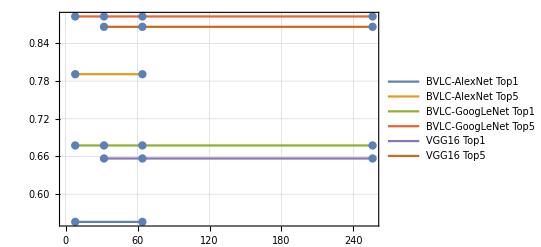

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

### Top1 / Top5 Model Accuracy on AMD64 & Minsky for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

-Graphics-

### Top1 / Top5 Model Accuracy on Minsky for Caffe2

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

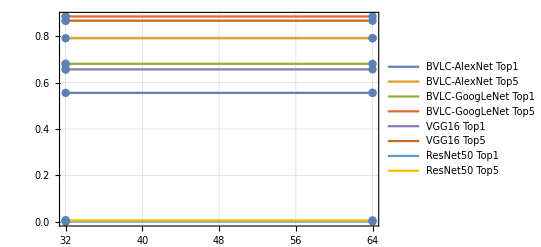

```mathematica
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Joined->True,
Mesh->All,
PlotTheme->"Detailed"
]
```

```mathematica
BarChart[
Catenate[
KeyValueMap[
Function[{key,val},
Join[
Table[<|ToString[e["BatchSize"]] <> " Top1"->Callout[e["Top1"],key <> " Top1"]|>,{e,val}],
Table[<|ToString[e["BatchSize"]] <> " Top5"->Callout[e["Top5"],key <> " Top5"]|>,{e,val}]
]
],
models
]],
ChartLabels->{32,64},
ChartLegends->Automatic,
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
Dataset[models]
```

Dataset[<>]

### Model Timing on Minsky for Caffe2

```mathematica
$DurationInformation;
```

```mathematica
Length[$DurationInformation]
```

24

```mathematica
models=GroupBy[$DurationInformation,Lookup["FrameworkModel"]];
```

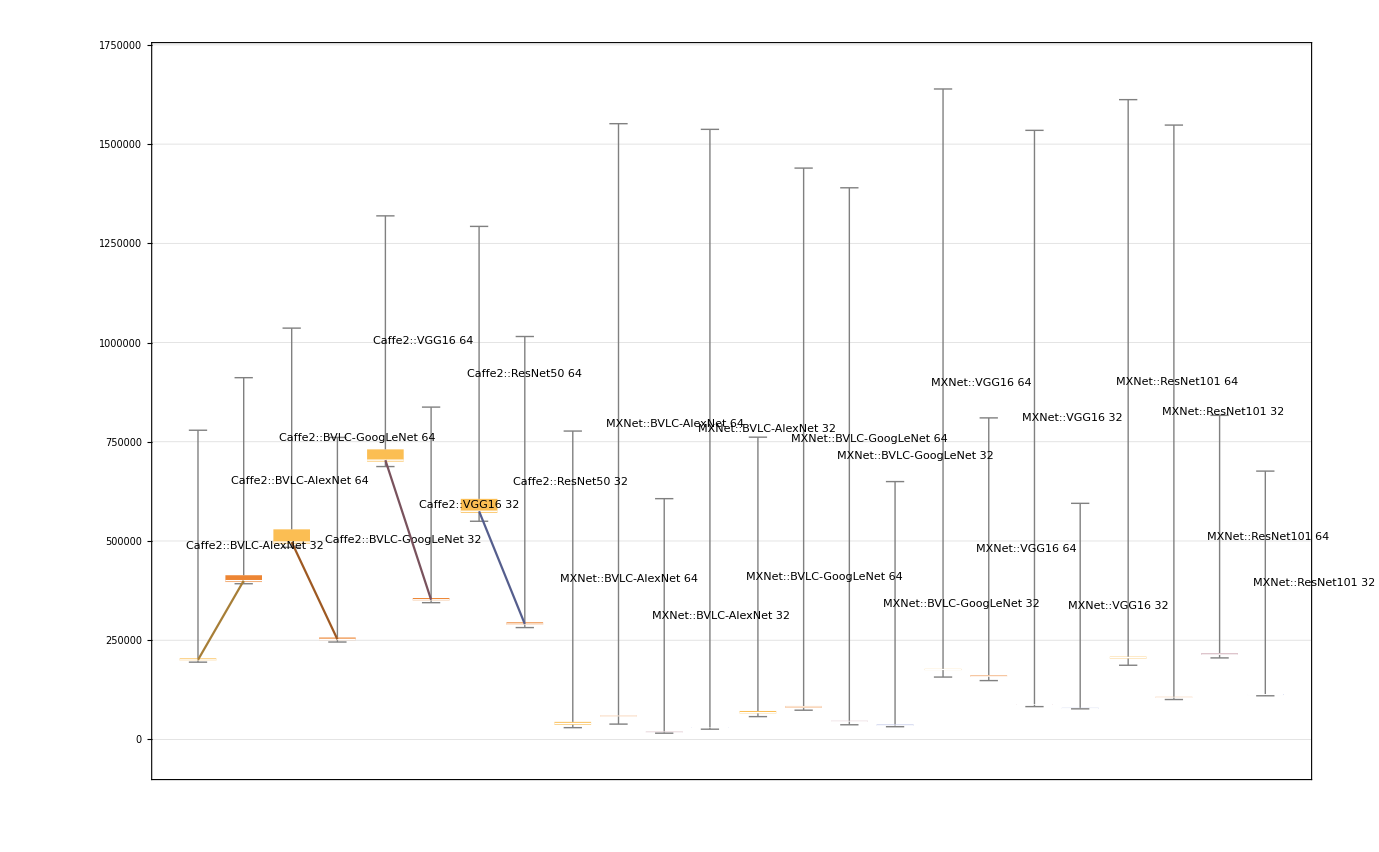

```mathematica
BoxWhiskerChart[
KeyValueMap[
Function[{key,val},
Table[
Labeled[e["Durations"],key <>" " <>ToString[e["BatchSize"]],Left,RotateLabel->True],
{e,val}
]
],
models
],
Joined->True,
LabelingFunction->Automatic,
PlotTheme->"Detailed"
]
```

```mathematica
ListPlot[
KeyValueMap[
Function[{key,val},
Legended[
Table[
Callout[{e["BatchSize"],Median[e["Durations"]]/e["BatchSize"]},
e["HostName"]<>"::"<>e["Framework"]<>"::"<>ToString[e["BatchSize"]]
],
{e,SortBy[val,#["BatchSize"]&]}
],
key
]
],
models
],
Mesh->All,
Joined->False,
Axes->True,
PlotTheme->"Grid",
AxesLabel->{"BatchSize","Median Time (us)"}
]
```

-Graphics-

```mathematica
ListPlot[
KeyValueMap[
Function[{key,val},
Legended[
Table[
duration=UnitConvert[Quantity[Median[e["Durations"]]/e["BatchSize"],"Microseconds"],"Milliseconds"];
Tooltip[
Callout[
{e["BatchSize"],duration},
e["HostName"]<>"::"<>e["Framework"]<>"::"<>ToString[e["BatchSize"]]
],
GeneralUtilities`Infobox[
<|
"HostName"->e["HostName"],
"MachineArchitecture"->e["MachineArchitecture"],
"UsingGPU"->e["UsingGPU"],
"Duration"->duration,
"BatchSize"->e["BatchSize"]
|>,
"Information"
]
],
{e,SortBy[val,#["BatchSize"]&]}
],
First[val]["Framework"]<> "/"<>key
]
],
models
],
Mesh->All,
Joined->False,
Axes->True,
PlotTheme->"Grid",
AxesLabel->{"BatchSize","Median Time (ms)"}
]
```

-Graphics-